## RQA Validation -

Flip Phillips, Aug 19

#### Intro

I am presently trying to validate my RQA package to Webber’s computations from the RQA151 code and included paper. Most of the measurements come out consistent with those in the paper. Some don’t and I’m trying to track that down.

The HENCX dataset included with the RQA151 distribution doesn’t seem to be the same as the one used in the chapter-

Webber Jr, C. L., & Zbilut, J. P. (2005). Recurrence quantification analysis of nonlinear dynamical systems. Tutorials in contemporary nonlinear methods for the behavioral sciences, 94, 26-94. https://www.nsf.gov/pubs/2005/nsf05057/nmbs/chap2.pdf

It looks like the pattern they used in that paper starts around t=42 ± so I just pulled the next 200 off of that. Here are the results from RQD.EXE:

Note that – even though the sequence is length 200, the rendered distance/recurrence matrix is 201x201... maybe it treats the data as periodic? I’m even further confused since, when embedding the data in a 3-D manifold, there are, by definition, only n-d+1 valid points in this space (again, unless there is some periodicity employed), so the real dimensionality of that should be 198x198, if anything.

```mathematica
<<RQA`
```

I screen-grabbed the RM (and inverted the colors so I could see it) —

```mathematica
wrm=-Graphics-;
```

```mathematica
ImageDimensions[wrm]
```

{201,201}

Here’s a recurrence map structure, derived from that image, which we can use to check some of the calculations:

```mathematica
rmx=RQARemoveLOI[SparseArray[1-Reverse@ImageData[Binarize[wrm]]]];
```

Secondly, I calculated the recurrence coordinates using RQC.EXE. I noted that the diagonal has ‘points’ but the distance is 0.0. This suggests to me that, like I mention above, I might be missing some 0-distance locations.

```mathematica
rpts=Import[ResourceFunction["NotebookRelativePath"]["HX"],"Table"];
```

```mathematica
Length[rpts]
```

764

```mathematica
dmx=RQARemoveLOI[SparseArray[#[[1;;2]]->#[[3]]&/@rpts]]
```

SparseArray[…]

```mathematica
ArrayPlot[dmx,DataReversed->True,PlotLegends->Automatic,FrameTicks->None,ColorFunction->ColorData["Temperature"]]
```

-Graphics-

But, maybe the recurrence matrix should have ‘1’s where those 0-locations are.

```mathematica
rmx2=RQARemoveLOI[SparseArray[#[[1;;2]]->1&/@rpts]];
```

```mathematica
ArrayPlot[rmx2,DataReversed->True,PlotLegends->Automatic,FrameTicks->None,ColorFunctionScaling->True,ColorFunction->ColorData[{"DarkTerrain","Reverse"}]]
```

-Graphics-

Notice that this array is 200x200. I’m guessing that there is no truncation post-embedding.

So, let' s compare my RQA with Webber 151.

### data

Load the data:

```mathematica
data=Import[ResourceFunction["NotebookRelativePath"]["HENXC"],"List"];
```

Create a time series:

```mathematica
hx=TimeSeriesWindow[TimeSeries[TemporalData[data,{1,Automatic,1},ValueDimensions->1]],{42,241}]
```

TimeSeries[…]

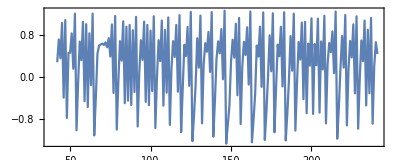

```mathematica
ListLinePlot[hx,Axes->None,Frame->True,AspectRatio->.4]
```

Close enough to this, from the paper (and, remember, I went ahead and ran the same analysis in RQD from RQA151 above too):

Statistical measures are the same, according to the RQD output:

```mathematica
Mean[hx]
```

0.251136

```mathematica
StandardDeviation[hx]
```

0.724491

```mathematica
MinMax[hx]
```

{-1.28101,1.27268}

### embedding and distance / recurrence maps

Embedding, 3D, τ =1:

```mathematica
hxe3=RQAEmbed[hx,3,1.0,"Truncate"->True]
```

TimeSeries[…]

Notice that we are using “Truncate” which makes the embedded time series a proper length with valid locations for the embedding. I should add “Periodic” maybe.

Distance matrix:

```mathematica
dm=RQADistanceMap[hxe3,DistanceFunction->EuclideanDistance];
```

```mathematica
ArrayPlot[dm,DataReversed->True,PlotLegends->Automatic,FrameTicks->None,ColorFunction->ColorData["Temperature"]]
```

-Graphics-

```mathematica
Dimensions[dm]
```

{198,198}

Range is the same as the RQD calculations, roughly:

```mathematica
MinMax[dm]
```

{0.,3.107}

Mean distances:

```mathematica
Mean[Flatten[dm]]
```

1.59558

Now, there is a normalizing step in the RQD that I don’t quite understand why. It scales to ‘maxdist’ which leads to some crazy distances reported in the output. It looks like it shifts distances to a range of 0-100. We’re just going to do 0-1 because I think that’s what’s going on, then we’ll treat distances appropriately.

If we do the rescale w/ the 200x200 map onto 0-100 like Webber, we get:

```mathematica
Mean[Rescale[Flatten[dm]]]*100
```

51.3545

His mean is 51.441, so there is something going on there. I wonder if there is an off-by-one or something, since the RQD matrix above is 201x201 and ours is 198x198 because of the embedding?

This computes the recurrence map for a given threshold distance. The paper uses a Radius=3 so on the 0-100 scale that’s:

```mathematica
rm=RQARecurrenceMap[hxe3,0.03,"Rescale"->True,DistanceFunction->EuclideanDistance];
```

Also, our rescale is just a generic minmax rescale. “RescaleFunction” gives you the ability to use different functions.

Here is a recurrence map which looks essentially the same as the one above. I’m not sure why all the Webber maps have the diagonal in place. For all of those locations, the distance is 0 and, I suppose, there is recurrence by definition? Perhaps this is the problem with my calculations below?

```mathematica
ArrayPlot[rm*dm,DataReversed->True,PlotLegends->Automatic,FrameTicks->None,ColorFunctionScaling->True,ColorFunction->ColorData[{"DarkTerrain","Reverse"}]]
```

-Graphics-

### parameter estimates

#### #recur

I’m doing these in the order that they are stated in the RQD output screen. Firstly, #recur  = 282, we get:

```mathematica
RQANRecurrentPoints[rm]
```

272

```mathematica
RQANRecurrentPoints[rmx]
```

281

This guy is right on:

```mathematica
RQANRecurrentPoints[rmx2]
```

282

These are all pretty close to double the actual points, so the prior art must take advantage of upper triangularization.

#### #lines

The output above gives us 54 total lines. I’m not sure which those are, diagonal, etc. Might be able to figure it out with our stuff here.

Vertical

```mathematica
RQANVerticalLines[rm]
```

2

Same for those in the RQC

```mathematica
RQANVerticalLines[rmx2]
```

2

```mathematica
RQANVerticalRecurrentPoints[rm]
```

4

```mathematica
RQANVerticalRecurrentPoints[rmx2]
```

4

Diagonal lines:

```mathematica
RQANDiagonalLines[rm]
```

53

```mathematica
RQANDiagonalLines[rmx2]
```

54

54 lines in double-world means 108 lines in reflection land.

```mathematica
RQANDiagonalRecurrentPoints[rm]
```

228

```mathematica
RQANDiagonalRecurrentPoints[rmx2]
```

235

#### Recurrence

RQD = 1.417%

```mathematica
RQARecurrence[rm]//N
```

0.0139466

```mathematica
RQARecurrence[rmx]//N
```

0.0139801

```mathematica
RQARecurrence[rmx2]//N
```

0.0141709

```mathematica
RQARecurrence[dmx]//N
```

0.0141709

so it looks like rmx2 is the ‘right’ data. We’ll use it for the rest of the festival

```mathematica
bleh=Table[k->RQARecurrence[rmx2,k],{k,1,First[Dimensions[rmx2]]/2}]//N
```

{1.→0.0000502538,2.→0.0000502563,3.→0.,4.→0.000100523,5.→0.,6.→0.,7.→0.,8.→0.000201086,9.→0.000100548,10.→0.,11.→0.000251395,12.→0.,13.→0.000402273,14.→0.,15.→0.,16.→0.000100583,17.→0.,18.→0.,19.→0.,20.→0.000201207,21.→0.000100609,22.→0.,23.→0.,24.→0.00025156,25.→0.000150943,26.→0.,27.→0.0000503195,28.→0.,29.→0.000100649,30.→0.,31.→0.,32.→0.0000503322,33.→0.,34.→0.,35.→0.,36.→0.,37.→0.000201379,38.→0.00020139,39.→0.0000503499,40.→0.000100705,41.→0.000050355,42.→0.,43.→0.,44.→0.000100725,45.→0.000201461,46.→0.,47.→0.,48.→0.,49.→0.0000503753,50.→0.,51.→0.000100761,52.→0.,53.→0.000100771,54.→0.,55.→0.,56.→0.,57.→0.,58.→0.000251991,59.→0.,60.→0.,61.→0.,62.→0.,63.→0.,64.→0.,65.→0.,66.→0.000100837,67.→0.,68.→0.,69.→0.,70.→0.,71.→0.,72.→0.,73.→0.000100873,74.→0.0000504388,75.→0.,76.→0.,77.→0.000302679,78.→0.,79.→0.,80.→0.,81.→0.,82.→0.000151378,83.→0.,84.→0.,85.→0.0000504668,86.→0.,87.→0.,88.→0.,89.→0.,90.→0.0000504796,91.→0.,92.→0.,93.→0.,94.→0.,95.→0.,96.→0.,97.→0.,98.→0.000101,99.→0.,100.→0.}

```mathematica
Values[bleh]//Total
```

0.00448095

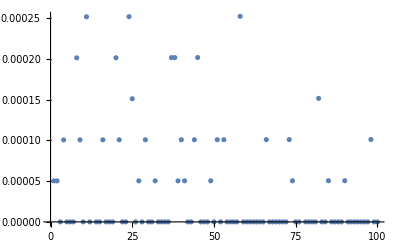

```mathematica
ListPlot[Values@%]
```

#### Determinism

RQD = 83.333%

```mathematica
RQADeterminism[rmx2]//N
```

0.833333

#### Ratio

```mathematica
RQARatio[rmx2]//N
```

OptionValue::nodef: Unknown option Dmin for RQA`Private`diagonalSegments.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

117.612

```mathematica
RQADeterminism[rmx2]/RQARecurrence[rmx2]//N
```

58.8061

So, according to the book, the scaling factor is n^2 but it should be n^2-n because of the LOI stuff. There is a lot of LOI inconsistency.

#### DMax

RQD = 14

```mathematica
RQADmax[rmx2]
```

14

```mathematica
RQADmean[rmx2]//N
```

4.35185

#### Entropy

RQD = 2.812

```mathematica
RQAEntropy[rmx2]//N
```

2.81211

#### RR_* Stuff

Diagonal-wise computations.

```mathematica
RQADApply[Length,rmx2]
```

108

```mathematica
Dimensions[rmx2]
```

{200,200}

#### Trend

TND = 1.841

```mathematica
RQATrend[rmx2]//N
```

0.0071606

This is way off.

#### Laminarity

RQD = 1.773%

```mathematica
RQALaminarity[rmx2]//N
```

0.0141844

#### Trapping Time

TT = 2.5

```mathematica
RQATrappingTime[rmx2]//N
```

2.

#### VMax

Vmax =3

```mathematica
RQAVmax[rmx2]
```

2